```mathematica
time = Accumulate[{0,23.13,24.05,24.6,26.41,26.46,42.37,27.89,23.22,26.96,21.97,25.78,30.92,27.16,23.6,34.67}];

counts = Log[{8781,7960,7201,6479,5610,5023,4051,3598,3416,2829,2640,2396,2172,1856,1603,1466}];
data = Transpose[{time,counts}];

f = Fit[data,{1,x},x]
p1 = ListPlot[data];
Show[Plot[f,{x,0,410},AxesLabel -> {"Time (s)","Log Counts"},PlotLabel -> "Ba-137 Decay"],p1]
```

9.07698-0.00443787 x

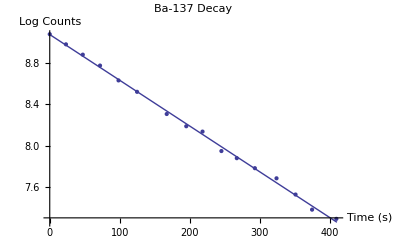
```mathematica
Export["BaDecay.eps",-Graphics-]
```

BaDecay.eps

```mathematica
Solve[9.076975747950256-0.004437874204435571 x==Log[.5*8781],x]
```

{{x→155.43}}